# Introduction to Wave Models

We have studied the phase space picture of single particle dynamics. As you have learned to think about the evolution of a paticle subject to external forces using the phase space picture, you have also been learning to use Mathematica to explore this kind of quantitative model. We are going to build on what you have learned so far in a number of diferent directions. One direction is to get out one dimensional motion and another is to break out in the much more interesting realm of systems of interacting particles. We will continue to use Mathematica to aid us in exporing these topics.

One simple generaliztion to many interacting (classical) particles is  the case of  a large system of particles held in a dynamic equilibrium configuration by interactions between each particle and its neighbors in space. Systems where the interactions between particles are only significant when the particles neighbor one another  are relatively easy to model because their behavior is simpler than what might otherwise occur where more interactions need to be taken into account. It is quite common to find systems of particles in nature held in semi-rigid stable configurations. These configurations have the properties that local disurbances from the equilibrium configuration of the particles propagate through the system. These propagating disturbances are generally referred to as ‘waves”. 

In this notebook I will lay out a simple model of inteacting particles along a line connected by ‘massless’ springs. We will use the methodologies I lay out here, and generalizations that you will invent yourself, to develop similar models of systems of particles in 2 and 3 space dimensions and also to explore the the behavior of continuous media.

TO START:  EITHER EVALUATE THE ENTIRE NOTEBOOK, (THIS WILL TAKE BETWEEN 3 and 10 MINUTES ON Most Computers)  or ALTERNATIVELY, EVALUATE AS YOU READ THROUGH THE NOTEBOOK. But make sure to evaluate all the input cells in order.

## Discrete Evolution Model

The model: Lots of little masses on a straight line,  each mass connected to its  two  neighbors by springs 

Recall that springs pull or push in proportion to their stretch or compression from their equilibrium length respectively, with a proportionality constant called the spring constant (k).

Uniform medium  : All masses the same (m) , all springs the same with the same spring constants (k), all equilibrium lengths of the springs  the same
         
omega2= k/m  - you will notice that this is the angular frequency for a simple harmonic oscillator, and sets the scale for effects of the nearest neighbor interactions
	
Δx_0 = equilibrium spacing ; we will choose  length units in which Δx_0 =1
	
We wil choose mass units in which all particle masses =1

Coming from our previous work with particles and phase space, you should imagine this as lots of little phase spaces coupled together

Here are the dynamical equations of out model. The index i refers to the ith particle, i = 1.....n number of particles.
Note: In the expression below, Δx_0 drops out of the acceleration  if the equilibrium lengths of all springs are all the same, i.e. the medium is uniform  

dx_i/dt = v_i   ;

dv_i/dt   = Force on ith particle /m =  a_i[ x_(i-1) , x_i, x_(i+1)] 
		= omega2 ( x_(i+1) -x_i -Δx_0) - omega2 (x_i -x_(i-1) -Δx_0)  
		= omega2 (  x_(i+1) + x_(i-1) - 2 x_i )

Just because I can't resist mentioning it here: it will eventually be useful to observe that     omega2 (  x_(i+1) + x_(i-1) - 2 x_i ) = ( omega2 (Δx_0)^2)   ((  x_(i+1) + x_(i-1) - 2 x_i )/(Δx_0)^2)
The first term in brackets in the last expression, omega2 (Δx_0)^2, has units of speed^2; while the second term in brackets is the discrete approximation for (ⅆ^2 ψ)/(ⅆ x^2) where ψ (x,t) is the distortion of the medium from equilibrium at position x, or perturbation of the medium. This is a little hard to visualize when the medium is constrained to 1 dimension but
not at all hard to understand when it is some other characteristic of the medium or where the medium can move more generally in space.

Models such as these require initial conditions AND boundary conditions ( in a general sense these are space-time boundary conditions...)

	Initial conditions : set all initial x_i and v_i in the phase space of  each particle

	Boundary Conditions : We will use the simplest possible boundary condtions:  x_1 and x_n(endpoints) are fixed

There are alternative boundary conditions that correspond to some different physical situations:e.g.  v is cloned at end points from nearest neighbors, or periodic boundary conditions; or even boundary conditons that correspond to something else interacting with the system  more generally at its endpoints throughout the system's evolution. We will discuss these alternatives after we have some experience with the simplest model in which we imagine the ends of our string of particles to be nailed down.

## Initialize a System State

```mathematica
initState[n_,x_,v_]:=Table[{x[i],v[i]},{i,1,n,1}];  (*initializes a state with n particles*)
omega2=1.0;  (*work in units with omega2 set to one...I have left this parameter in the rest of the development so you can play with larger or smaller omega2...this number sets the size of the interaction between adjacent particles*)

testState=initState[200,(#-100)+10Sin[2 Pi (#-100)/100]Exp[-(#-100)^2 /400]&,0*#&]; 
(*Large Distortion in space near the center and zero inital velocities, so there is a lot of stored up potential energy in the springs near the center when we start the psrticles from rest ( with zero initial velocity) at t=0*)
```

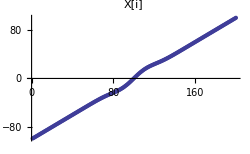
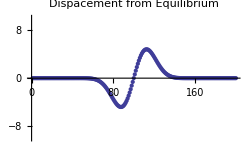
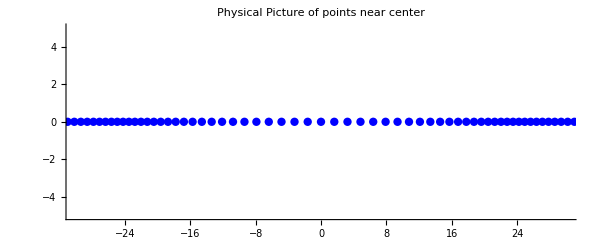
Take a look at the initial state
-Graphics--Graphics--Graphics-

```mathematica
Pane[Column[{"Take a look at the initial state",
Row[{ListPlot[Table[First[testState[[i]]],{i,1,Length[testState],1}],ImageSize->250,PlotLabel->"X[i]"],
ListPlot[Table[First[testState[[i]]]-(i-100),{i,1,Length[testState],1}],PlotRange->{-10,10},ImageSize->250,PlotLabel->"Dispacement from Equilibrium"],
Show[Graphics[{Blue,PointSize[.01],Point[testState]}],Axes->True,PlotRange->{{-30,30},{-5,5}},ImageSize->600,PlotLabel->"Physical Picture of points near center"]
}]}],Scrollbars->True]
```

## Step - Wise Evolution Code

### Getting Acceptable Scaling Behavior from Time Step Code

Shown below is the simplest evolution step code we could imagine using,  but if we test it we would find that energy is not conserved in the model evolution for very long - e.g. we would get
energy growing at a small but noticable rate. 
(*s is a list of lists of form {x,v}
s[[i,1]]→x
s[[i,2]]→v*)
evolveState[s_, dt_, omega2_] := Module[{n = Length[s]},
   Table[If[(i == 1) || (i == n), {s[[i, 1]], 0},(*endpoints are fixed*) {s[[i, 1]] + dt*s[[i, 2]], s[[i, 2]] + dt*omega2*(s[[i + 1, 1]] + s[[i - 1, 1]] - 2.0*s[[i, 1]])}], {i, 1, n}]];

#### We can do much better by using "2nd order code" that uses better estimates for the average acceleration and average velocity of each particle during each time step.

```mathematica
(*Use a compiled function for better computation performance in each evolution step and Code that is second order to reduce error*)
compiledf=Compile[{dt,omega2,x,v,bx,bv,ax,av},Module[{newv=v+dt*omega2*(ax+bx-2.0*x+0.5*dt*(av+bv-2.0*v))},{x+0.5*dt*(v+newv),newv}],CompilationTarget->"C"];
(*estimate the time average acceleration using an estimate for poeitions at midpoint of evolution step, evolve x with average of initial and final velocities = enforce assumption of approximately constant acceleration during time step*)
```

#### We apply our evolution step code to every particle in the system to evolve the whole system of particles forward in each time step

```mathematica
betterEvolveState[s_,dt_Real,omega2_]:=Module[{n=Length[s]},
Table[If[((i==1)||(i==n)),{s[[i,1]],0.0},compiledf[dt,omega2,s[[i,1]],s[[i,2]],s[[i-1,1]],s[[i-1,2]],s[[i+1,1]],s[[i+1,2]]]],{i,1,n,1}]];
(*Using Fixed end Boundary Conditions*)
```

### Creating a History Using NestList and Step - Wise Evolution Code

#### Applying evolution step to the whole system over and over using NestList to produce a history list of states of the system of particles:

```mathematica
betterHist[steps_,dt_,omega2_,initS_]:=NestList[
betterEvolveState[#,dt,omega2]&,initS,steps];
```

#### Generating a history with 20000 steps @ .02 time units per step for a total duration of 400 time units

```mathematica
evolutionStepCount=20000;
evolutionStepSize=0.02;
testHist=betterHist[evolutionStepCount,evolutionStepSize,omega2,testState];
```

## Assessing The State of the System at an instant of time

### Functions to Assess Local and Global Properties

```mathematica
(*Displacement of Particles from Equilibrium*)
(*looks like we're assuming that the masses are 1 unit apart *)
amplitude[s_]:=Module[{n=Length[s]},Table[If[(i==1)||(i==n),{s[[i,1]],0},{s[[i,1]],s[[i,1]]-(i-100)}],{i,1,n}]];

(*Particle density*)
density[s_]:=Module[{n=Length[s]},Table[If[(i==1)||(i==n),{s[[i,1]],0},{s[[i,1]],2/(-s[[i-1,1]]+s[[i+1,1]])}],{i,1,n}]];

(*Momentum density*)
momentumDensity[s_]:=Module[{n=Length[s]},Table[If[(i==1)||(i==n),{s[[i,1]],0},{s[[i,1]],2*s[[i,2]]/(-s[[i-1,1]]+s[[i+1,1]])}],{i,1,n}]];

(*total System Momentum*)
(*add up velocities *)
sysMomentum[s_]:=Sum[s[[i,2]],{i,2,Length[s]-1}];

(*Kinetic energy Density*)
(*velocity squared over distance *)
kineticEnergyDensity[s_]:=
Module[{n=Length[s]},Table[If[(i==1)||(i==n),{s[[i,1]],0},{s[[i,1]],s[[i,2]]*s[[i,2]]/(-s[[i-1,1]]+s[[i+1,1]])}],{i,1,n}]];

(*Total System paticle energy = Kinetic energy*)
(*(1/2)mv^2 *)
sysKineticEnergy[s_]:=Sum[0.5*(s[[i,2]]^2),{i,1,Length[s]}];

(*Interaction = Potential Energy Density *)
potentialEnergyDensity[s_,omega2_]:=
Module[{n=Length[s]},Table[If[(i==1)||(i==n),{s[[i,1]],0},{s[[i,1]],(0.25*omega2(s[[i,1]]-s[[i-1,1]]-1.0)^2+0.25*omega2*(s[[i+1,1]]-s[[i,1]]-1.0)^2)/(-s[[i-1,1]]+s[[i+1,1]])}],{i,1,n}]];

(*System Potnetial Energy*)
sysPotentialEnergy[s_,omega2_]:=Sum[0.5*omega2*(s[[i,1]]-s[[i-1,1]]-1.0)^2,{i,2,Length[s]}];

totalEnergyDensity[s_,omega2_]:=Module[{tk=kineticEnergyDensity[s],tp=potentialEnergyDensity[s,omega2]},
Table[{tk[[i,1]],tk[[i,2]]+tp[[i,2]]},{i,1,Length[tk]}]
];
```

## Time Series Data for Assessement of Total System Properties

```mathematica
timeSeriesMomentum=Map[sysMomentum,testHist];
timeSeriesKineticEnergy=Map[sysKineticEnergy,testHist];
timeSeriesPotentialEnergy=Map[sysPotentialEnergy[#,omega2]&,testHist];
timeSeriesTotalEnergy=timeSeriesPotentialEnergy+timeSeriesKineticEnergy;
```

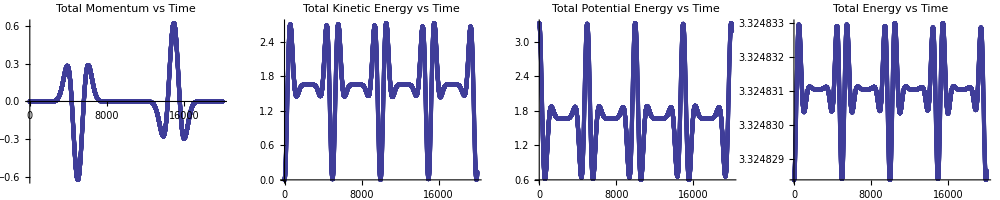

```mathematica
GraphicsRow[{ListPlot[timeSeriesMomentum,PlotLabel->"Total Momentum vs Time",PlotRange->All],ListPlot[timeSeriesKineticEnergy,PlotLabel->"Total Kinetic Energy vs Time",PlotRange->All],ListPlot[timeSeriesPotentialEnergy,PlotLabel->"Total Potential Energy vs Time" ,PlotRange->All],ListPlot[timeSeriesTotalEnergy,PlotLabel->"Total Energy vs Time",PlotRange->All]},ImageSize->{1000,200}]
(*TOTAL ENERGY: IT'S FLUCTUATING*)
```

#### Note that total energy variation is below the reported resolution of the numbers in the last graph. So our model conserves energy, at least up to 20000 steps.

## Looking at Evolving Local Properties of the System over a history

#### Evaluate all these Manipulates

```mathematica
a=Manipulate[ListLinePlot[amplitude[testHist[[i]]],PlotRange->{{-100,100},{-10,10}},PlotLabel->"Displacement from Equilibrium",AxesLabel->{"X","δX"}],{{i,1,"Time Step"},1,Length[testHist]}];
d=Manipulate[ListLinePlot[density[testHist[[i]]],PlotRange->{{-100,100},{.5,3}},PlotLabel->"Density Plot - Particles per unit length",AxesLabel->{"X","particles/length"}],{{i,1,"Time Step"},1,Length[testHist]}];
p=Manipulate[ListLinePlot[momentumDensity[testHist[[i]]],PlotRange->{{-100,100},{-.5,.5}},PlotLabel->"Linear Momentum/Unit Length"],{{i,1,"Time Step"},1,Length[testHist]}];
k=Manipulate[ListLinePlot[kineticEnergyDensity[testHist[[i]]],PlotRange->{{-100,100},{0,.2}},PlotLabel->"Kinetic Energy Density"],{{i,1,"Time Step"},1,Length[testHist]}];
u=Manipulate[ListLinePlot[potentialEnergyDensity[testHist[[i]],omega2],PlotRange->{{-100,100},{-.3,.3}},PlotLabel->"Potentila Energy Density"],{{i,1,"TimeStep"},1,Length[testHist]}];
e=Manipulate[ListLinePlot[totalEnergyDensity[testHist[[i]],omega2],PlotRange->{{-100,100},{-.25,.25}},PlotLabel->"Total Energy Densty"],{{i,1,"TmeStep"},1,Length[testHist]}];
alle=Manipulate[ListLinePlot[{totalEnergyDensity[testHist[[i]],omega2],potentialEnergyDensity[testHist[[i]],omega2],kineticEnergyDensity[testHist[[i]]]},PlotRange->{{-100,100},{-.3,.3}},PlotLabel->"Energy Densities",PlotStyle->{{Red,Thick},{Blue,Thick,Dashed},{Purple,Thick,Dashed}},PlotLegends->{"Total Energy Density","Potential Energy Density","Kinetic Energy Density"}],{{i,1,"TmeStep"},1,Length[testHist]}];
Pane[Grid[{{Style["Examining The Model","Section"],SpanFromLeft},{a,d},{p,k},{u,alle}},Alignment->Center],ImageSize->{1100,1100},Scrollbars->True]
```

Examining The Model | 
 | 
 | 
 |

Part::partd: Part specification testHist ⟦ 9100. ⟧ is longer than depth of object.

ListLinePlot::lpn: amplitude[testHist ⟦ 9100. ⟧] is not a list of numbers or pairs of numbers.

Part::partd: Part specification testHist ⟦ 1 ⟧ is longer than depth of object.

ListLinePlot::lpn: density[testHist ⟦ 1 ⟧] is not a list of numbers or pairs of numbers.

Part::partd: Part specification testHist ⟦ 1. ⟧ is longer than depth of object.

ListLinePlot::lpn: momentumDensity[testHist ⟦ 1. ⟧] is not a list of numbers or pairs of numbers.

Part::partd: Part specification testHist ⟦ 1 ⟧ is longer than depth of object.

ListLinePlot::lpn: kineticEnergyDensity[testHist ⟦ 1 ⟧] is not a list of numbers or pairs of numbers.

Part::partd: Part specification testHist ⟦ 1 ⟧ is longer than depth of object.

ListLinePlot::lpn: potentialEnergyDensity[testHist ⟦ 1 ⟧, omega2] is not a list of numbers or pairs of numbers.

Part::partd: Part specification testHist ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification testHist ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partd: Part specification testHist ⟦ 9100. ⟧ is longer than depth of object.

ListLinePlot::lpn: amplitude[testHist ⟦ 9100. ⟧] is not a list of numbers or pairs of numbers.

Part::partd: Part specification testHist ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

## The Space - Time Picture

### Creating an interpolation function for displacement from equilibrium as a function of time = : ψ[x, t]

```mathematica
vals=Table[testHist[[i,j,1]]-(j-100),{i,1,Length[testHist],1},{j,1,200,1}];
isol=ListInterpolation[vals,{{0,400},{-100,100}},InterpolationOrder->2];
Plot3D[isol[t,x],{t,0,evolutionStepCount*evolutionStepSize},{x,-99,100},PlotRange->{-10,10},AxesLabel->{"T","X","ψ[t,x]"},PlotPoints->100]
```

-Graphics3D-

## Using NDSolve to Solve the (Continuum) Wave Equation

```mathematica
(*Woah what is this "continuum waves equation
u is displacement from equilibrium
(∂^2 u)/(∂x^2)==c^2(∂^2 u)/(∂t^2), 
ψ[0,x]==Sin[2*Pi *x/10] ⅇ^(-x^2/4)
ψ^(1,0)[0,x]==0 partial derivative with (1,0) at (0, x)
ψ[t,-10]==0 boundary!
ψ[t,10]==0 boundary!
*)
```

```mathematica
c=1.0;
ndsol=NDSolve[{D[ψ[t,x], t,t]==c^2  D[ψ[t,x], x,x],ψ[0,x]==Sin[2*Pi *x/10] ⅇ^(-x^2/4),Derivative[1,0][ψ][0,x]==0,ψ[t,-10]==0,ψ[t,10]==0},ψ,{t,0,40},{x,-10,10},StartingStepSize->.01,MaxSteps->100000]
```

{{ψ→InterpolatingFunction[{{0.,40.},{-10.,10.}},<>]}}

```mathematica
Manipulate[Plot[Evaluate[ψ[t,x]/.First[ndsol]],{x,-10,10},PlotRange->{-1,1}],{t,0.0,40.0}]
```

First::normal: Nonatomic expression expected at position 1 in First[ndsol].

ReplaceAll::reps: {First[ndsol]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

## The Space - Time Picture

```mathematica
Plot3D[Evaluate[ψ[t, x] /. First[ndsol]], {x, -10, 10}, {t, 0, 40}, PlotRange->{-1,1},AxesLabel -> {Style["X = Space",Larger,Bold], Style["T= Time" ,Larger,Bold], Style["u[x,t] - Disp from Equilibrium",Larger,Bold]},ImageSize->600,AspectRatio->1,PerformanceGoal->"Quality",PlotPoints->100]
```

-Graphics3D-